```mathematica
<<MaTeX`
totald431=10*5000000;
d431pPOT=1.2*10^-6;
ncm2=700*300;
POTpyear=1.47*10^21;
(*POTpyear=10^20;*)
d431factor=1/totald431*d431pPOT*POTpyear*1/ncm2
```

168.

## Energy plot

### Data

```mathematica
nudata=Import[NotebookDirectory[]<>"data-e.dat"];
nubardata=Import[NotebookDirectory[]<>"databar-e.dat"];
nutable={};
Do[
bwidth=(nudata[[i,3]]-nudata[[i,2]])/nudata[[i,1]];
xrange=N[Table[nudata[[i,2]]+q*bwidth,{q,0,nudata[[i,1]]}]];
AppendTo[nutable,N[Table[{xrange[[l]],nudata[[i,3+l]]/bwidth*d431factor},{l,1,nudata[[i,1]]}]]];
,{i,1,41*3}]
nubartable={};
Do[
bwidth=(nubardata[[i,3]]-nubardata[[i,2]])/nubardata[[i,1]];
xrange=N[Table[nubardata[[i,2]]+q*bwidth,{q,0,nubardata[[i,1]]}]];
AppendTo[nubartable,N[Table[{xrange[[l]],nubardata[[i,3+l]]/bwidth*d431factor},{l,1,nubardata[[i,1]]}]]];
,{i,1,41*3}]
f[offaxis_,flavour_]:=nutable[[offaxis*3+flavour]];
fbar[offaxis_,flavour_]:=nubartable[[offaxis*3+flavour]];
```

### MaTeX

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
latexnue=MaTeX["\\nu_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumu=MaTeX["\\nu_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutau=MaTeX["\\nu_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
latexnuebar=MaTeX["\\bar{\\nu}_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumubar=MaTeX["\\bar{\\nu}_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutaubar=MaTeX["\\bar{\\nu}_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["E_{\\nu} \\text{(GeV)}",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["\\nu/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
ylabelbar=MaTeX["\\bar{\\nu}/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
```

### Plots nu

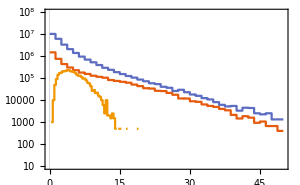

/home/sane/mainhnlchain/bg/120/analysis/energy-0.pdf

```mathematica
offaxis =0;
latext1=MaTeX["\\text{Off-axis="<>ToString[NumberForm[offaxis,{2,1}]]<>" m}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.05,0.9}],{-1,0}]];
framelabel={xlabel,ylabel};
frametickstyle=Directive[Black];
plotstyle=Opacity[1.0];
imagesize={300,Automatic};
plotrange={{0,50},{10,1*10^8}};
yticks={{10^1,"10"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"}};
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
legends={latexnue,latexnumu,latexnutau};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.1],{0.9,0.82}];
plot1=ListStepPlot[{f[offaxis,1],f[offaxis,2],f[offaxis,3]},PlotTheme->"Scientific",FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->White,FrameTicks->frameticks];
plotexp=Show[plot1,text]
Export[NotebookDirectory[]<>"energy-"<>ToString[offaxis]<>".pdf",plotexp]
```

### Plots nubar

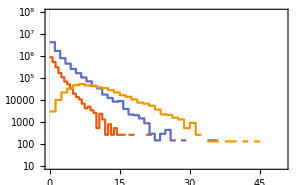

/home/sane/mainhnlchain/bg/120/analysis/energybar-40.pdf

```mathematica
offaxis=40;
latext1=MaTeX["\\text{Off-axis="<>ToString[NumberForm[offaxis,{2,1}]]<>" m}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.05,0.9}],{-1,0}]];
framelabel={xlabel,ylabelbar};
legends={latexnuebar,latexnumubar,latexnutaubar};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.1],{0.9,0.82}];
plotstyle={Opacity[1.0]};
yticks={{10^1,"10"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"}};
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
plot2=ListStepPlot[{fbar[offaxis,1],fbar[offaxis,2],fbar[offaxis,3]},PlotTheme->"Scientific",FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->White,FrameTicks->frameticks];
plotexp=Show[plot2,text]
Export[NotebookDirectory[]<>"energybar-"<>ToString[offaxis]<>".pdf",plotexp]
```

## Backup

```mathematica
plotid={1,2,3};
tablelegend1=Table[ToString[12+2*(plotid[[i]]-1)],{i,1,Dimensions[plotid][[1]]}];
```

```mathematica
plotid={1,2,3};
tableplot1=Table[nutable[[plotid[[i]]]],{i,1,Dimensions[plotid][[1]]}];
tableplot2=Table[nubartable[[plotid[[i]]]],{i,1,Dimensions[plotid][[1]]}];
```

### Data

```mathematica
nudata=Import[NotebookDirectory[]<>"data-e.dat"];
nubardata=Import[NotebookDirectory[]<>"databar-e.dat"];
nutable={};
nubartable={};
Do[
xmin=0;
xmax=50;
xrange=N[Table[xmin+q*(xmax)/nbins,{q,0,nbins}]];
If[Mod[i,3]==1,
xmin=0;
xmax=50;
nbins=40;
bwidth=(xmax-xmin)/nbins;
xrange=N[Table[xmin+q*(xmax)/nbins,{q,0,nbins}]]];
If[Mod[i,3]==2,
xmin=0;
xmax=50;
nbins=40;
bwidth=(xmax-xmin)/nbins;
xrange=N[Table[xmin+q*(xmax)/nbins,{q,0,nbins}]]];
If[Mod[i,3]==0,
xmin=0;
xmax=20;
nbins=60;
bwidth=(xmax-xmin)/nbins;
xrange=N[Table[xmin+q*(xmax)/nbins,{q,0,nbins}]]];
AppendTo[nutable,Table[{xrange[[l]],nudata[[i,l]]/bwidth*d431factor},{l,1,nbins}]];
AppendTo[nubartable,Table[{xrange[[l]],nubardata[[i,l]]/bwidth*d431factor},{l,1,nbins}]];
,{i,1,123}]
f1[offaxis_,flavour_]:=nutable[[offaxis*3+flavour]];
f2[offaxis_,flavour_]:=nubartable[[offaxis*3+flavour]];
```